***Exercise 1:

```mathematica
Plot3D[x^2 y,{x,-1,1},{y,-1,1.0},PlotRange->{-1,1}]
```

-Graphics3D-

Graph 1

```mathematica
Plot3D[x+y,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

Graph 2, starting at the origin if we are to move in the negative x and y direction we will decrease in z position, if we go in the positive x direction and  and go in the negative y direction or vice versa we will stay at y=0, finally by going in any direction who’s more positive than negative ie (++x,-y), (-x,++y,) or (+x,+y) we will increase height in the z direction

```mathematica
Plot3D[(x^2-y^2)/(x^2+y^2),{x,-3,3},{y,-3,3}]
```

-Graphics3D-

Graph 3

```mathematica
Plot3D[ⅇ^(-x^2-y^2),{x,-5,5},{y,-5,5},PlotRange->{0,1}]
```

-Graphics3D-

Graph 4

```mathematica
d[x_,y_]=(Sin[x])*(Cos[y])
Plot3D[d[x,y],{x,-2.,2.},{y,0,6}]
```

Cos[y] Sin[x]

-Graphics3D-

Graph 5

```mathematica
Plot3D[(-x^2+y^2)^4,{x,-2.,2},{y,-2,2.},PlotRange->{0,300}]
```

-Graphics3D-

Graph 6

***Exercise 3: to get evenly spaced lines I had to square root the x^2 and y^2

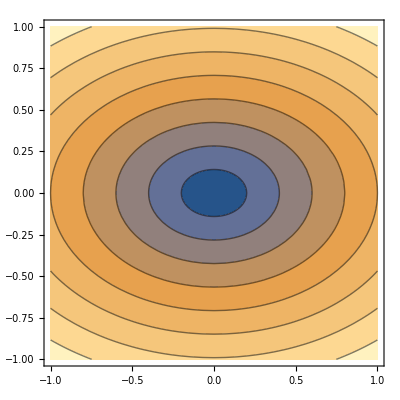

```mathematica
ContourPlot[Sqrt[x^2+2*y^2],{x,-1,1},{y,-1,1}]
```

***Exercise 6: to move the vertex over one unit to the right from the origin, I had to change x to (x-1). To move the vertex one unit in the y direction I changed y into (y-1).  To move the vertex up two units in the z direction I adjusted z to (z-2). Finally since the vertex starts two units above the origin if we want to increase the radius at the origin we can multiply z by a constant factor, in our case it was a constant of 4.

```mathematica
ContourPlot3D[
4*(z-2)^2==(x-1)^2+(y-1)^2,{x,-8,8},{y,-8,8},{z,-3,6},
Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-